```mathematica
(* Plotting package *)
<<MaTeX`
SetOptions[MaTeX,"Preamble"->{"\\usepackage{color,txfonts,amsbsy}"}];
<<ErrorBarLogPlots`(*Current fluctuations lower bound*)
(*DissipationAna=Import[NotebookDirectory[]<>"../data/Dissipation_Temperature.mat"][[1]];*)
DissipationKDE=Import[NotebookDirectory[]<>"../../data/KDEdissipation.mat"];
(*Changing temperature for 100 or 500*)
(*datalength varies from 12s to 12000s*)
(*Nspace is the stroboscopic size, like 50 means taking every 50 points*)
Nspace = 5;
temperature=500;
```

```mathematica
DissipationKDEPlot=Table[
{Mean[Transpose[DissipationKDE[[i]]][[-1]]],Mean[Transpose[DissipationKDE[[i]]][[1]]],StandardDeviation[Transpose[DissipationKDE[[i]]][[1]]]/Sqrt[10]}
,{i,1,4}];
```

```mathematica
(*Changing temperature for 100 or 500*)
(*datalength varies from 12s to 12000s*)
(*Nspace is the stroboscopic size, like 50 means taking every 50 points*)
KDEtime=(*Table[*)
Table[
temp=Table[
If[datalength==12000,CurFluc=Flatten[Import[NotebookDirectory[]<>"../../data/TwoBeadsConvergence/CurFluc_2D_trick_"<>ToString[temperature]<>"_"<>ToString[datalength]<>"_"<>ToString[count] <>"_"<>ToString[Nspace] <>".mat"]],CurFluc=Flatten[Import[NotebookDirectory[]<>"../../data/TwoBeadsConvergence/CurFluc_2D_"<>ToString[temperature]<>"_"<>ToString[datalength]<>"_"<>ToString[count] <>"_"<>ToString[Nspace] <>".mat"]]
];
If[datalength==12000,
CurFluc[[-1]]/500,
CurFluc[[-1]]/datalength]
,{count,1,10}];
{Nspace,datalength,temp}
,{datalength,{12,120,1200,12000}}];
(*,{Nspace,{5,10,50}}];*)

KDEtimePlot=(*Table[*)
Table[
{KDEtime[[i,2]],Mean[KDEtime[[i]][[-1]]](*/DissipationAna[[temperature/10-1,-1]]*),StandardDeviation[KDEtime[[i]][[-1]]]/Sqrt[10](*/DissipationAna[[temperature/10-1,-1]]*)}
,{i,1,4}];
(*,{j,1,3}];*)
```

```mathematica
(*
(*Changing temperature for 100 or 500*)
(*datalength varies from 12s to 12000s*)
(*Nspace is the stroboscopic size, like 50 means taking every 50 points*)
KDEspace=(*Table[*)
Table[
temp=Flatten[Import[NotebookDirectory[]<>"../data/TwoBeadsConvergence/KDE_"<>ToString[temperature]<>"_"<>ToString[datalength]<>"_"<>ToString[Nspace] <>".mat"]];
{Nspace,datalength,temp}
,{datalength,{12,120,1200,12000}}];
(*,{Nspace,{5,10,50}}];*)

KDEspacePlot=(*Table[*)
Table[
{KDEspace[[i,2]],Mean[KDEspace[[i]][[-1]]],StandardDeviation[KDEspace[[i]][[-1]]]}
,{i,1,4}];
(*,{j,1,3}];*)
*)
```

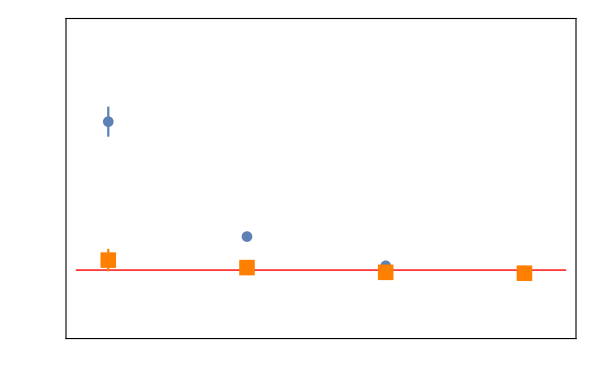

```mathematica
ymax = 10;
ymajor = 5;
yminor = 1;
ticksize = 18;
SpatialTemporalPlot = Show[
LogLinearPlot[
2.025,{x,7,24000},PlotStyle->{Red,Thick},
PlotRange->{{7,24000},{0,ymax}}
],


ErrorListLogLinearPlot[
DissipationKDEPlot,
(*PlotMarkers->{{●,15}},*)
PlotRange->{{7,24000},{0,ymax}}
],

ListLogLinearPlot[
Transpose[Transpose[KDEtimePlot][[1;;2]]],
PlotMarkers->{{■,16}},
PlotStyle-> Orange,
PlotRange->{{7,24000},{0,ymax}}
],
ErrorListLogLinearPlot[
KDEtimePlot,
(*PlotMarkers->{{●,10}},*)
PlotStyle-> Orange,
PlotRange->{{7,24000},{0,ymax}}
],

ImageSize->600,
ImagePadding->{{70, 10}, {75, 10}},
Frame->True,
FrameTicks-> {
Join[
{
(*{Log[1], MaTeX["0", FontSize->ticksize], {0.01,0}},*)
{Log[10], MaTeX["10^1", FontSize->ticksize], {0.01,0}},
{Log[100], MaTeX["10^2", FontSize->ticksize],  {0.01,0}},
{Log[1000], MaTeX["10^3", FontSize->ticksize],  {0.01,0}},
{Log[10000], MaTeX["10^4", FontSize->ticksize],  {0.01,0}}
},
Table[{Log[i 1],"", {0.005,0}},{i, 5, 9, 1}],
Table[{Log[i 10],"", {0.005,0}},{i, 1, 9, 1}],
Table[{Log[i 100],"", {0.005,0}},{i, 1, 9, 1}],
Table[{Log[i 1000],"", {0.005,0}},{i, 1, 9, 1}],
Table[{Log[i 10000],"", {0.005,0}},{i, 1, 2, 1}]
], 
Join[
Table[{i, MaTeX[i, FontSize->ticksize], {0.01,0}}, {i, 0,ymax, ymajor}],
Table[{i, "", 0.005}, {i, 0, ymax, yminor}]
],
Join[
{
{Log[10], "", {0.01,0}},
{Log[100],"",{0.01,0}},
{Log[1000], "", {0.01,0}},
{Log[10000], "", {0.01,0}}
},
Table[{Log[i 1],"",{0.005,0}},{i, 5, 9, 1}],
Table[{Log[i 10],"", {0.005,0}},{i, 1, 9, 1}],
Table[{Log[i 100],"", {0.005,0}},{i, 1, 9, 1}],
Table[{Log[i 1000],"", {0.005,0}},{i, 1, 9, 1}],
Table[{Log[i 10000],"", {0.005,0}},{i, 1, 2, 1}]
], 
Join[
Table[{i, "", {0.01,0}}, {i, 0, ymax, ymajor}],
Table[{i, "",{0.005,0}}, {i, 0, ymax, yminor}]
]
},
FrameLabel->{MaTeX["\\text{Trajectory Length} \\ \\tau_{\\rm obs}",FontSize->24],MaTeX["\\text{Dissipation Rate Estimate} \\quad \widehat{\\dot S }_{\\rm ss}",FontSize->24]}
]
```

```mathematica
Export[NotebookDirectory[]<>"SpatialTemporalPlot.pdf", SpatialTemporalPlot];
```